3/4

3

0

5

ⅇ^(-3 x^2)

-6 ⅇ^(-3 x^2) x

(HypergeometricPFQ[{1/2,1},{5/8,9/8},-3 x^2]/x^(3/4)-256/15 x^(5/4) HypergeometricPFQ[{3/2,2},{13/8,17/8},-3 x^2])/Gamma[1/4]

-1/(x^(3/4) Gamma[1/4])+(HypergeometricPFQ[{1/2,1},{5/8,9/8},-3 x^2]/x^(3/4)-256/15 x^(5/4) HypergeometricPFQ[{3/2,2},{13/8,17/8},-3 x^2])/Gamma[1/4]

((4 Gamma[9/8] Hypergeometric1F1[3/8,1/2,-3 x^2])/3^(1/8)-3^(3/8) x Gamma[5/8] Hypergeometric1F1[7/8,3/2,-3 x^2])/Gamma[1/4]

(-3^(3/8) Gamma[5/8] Hypergeometric1F1[7/8,3/2,-3 x^2]-6 3^(7/8) x Gamma[9/8] Hypergeometric1F1[11/8,3/2,-3 x^2]+7/2 3^(3/8) x^2 Gamma[5/8] Hypergeometric1F1[15/8,5/2,-3 x^2])/Gamma[1/4]

ConditionalExpression[-(6 (-1/16 3^(3/8) Gamma[-3/8] Hypergeometric1F1[7/8,1/2,-3 x^2]+3^(7/8) x Gamma[9/8] Hypergeometric1F1[11/8,3/2,-3 x^2]))/Gamma[1/4], Re[x]>0&&Im[x]==0]

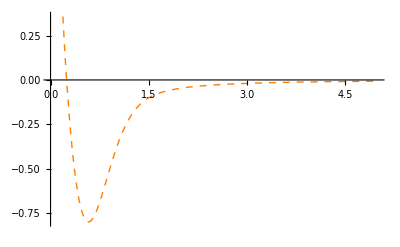

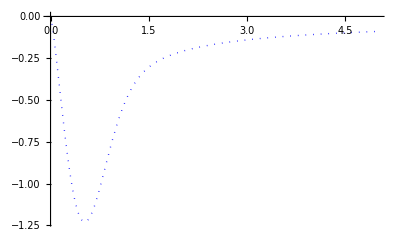

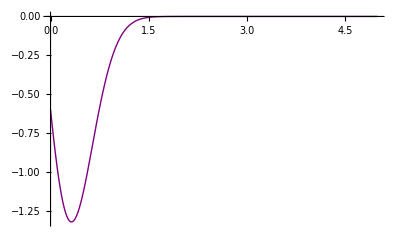

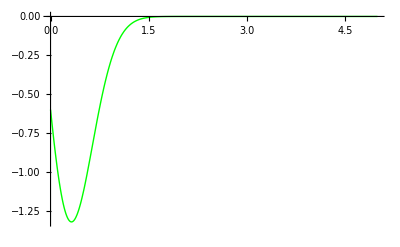

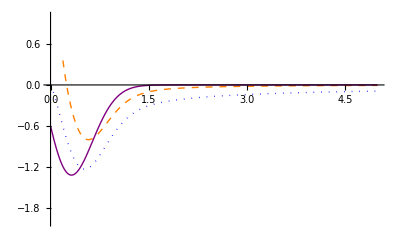

```mathematica
(*Input parameters*)
alpha=75/100                               (*alpha*)
k=3                             (*k>0 in e^(k x)*)
lb=0                            (*plot lower bound*)
ub=5                         (*plot upper bound*)
(*Riemann official *)
fun[x_] = Exp[-k x^2]
dfun[x_] = D[fun[x],x]
rieMat=FractionalD[fun[x],{x,alpha}]
(*Caputo official *)
capMat=CaputoD[fun[x],{x,alpha}]
(*Liouville *)
i1 = 1/Gamma[1-alpha]Integrate[(xi-x)^(-alpha)fun[xi],{xi,x,Infinity}]
lio = D[i1,x]
(*LiouvilleInvert *)
i2 = 1/Gamma[1-alpha]Integrate[(xi-x)^(-alpha)dfun[xi],{xi,x,Infinity}]
(*pot routines*)
pR1=Plot[rieMat,{x,lb,ub},PlotStyle->{Orange,Dashed,Thick}]
pC1=Plot[capMat,{x,lb,ub},PlotStyle->{Blue,Dotted,Thick},PlotRange->All]
pL1=Plot[lio       ,{x,lb,ub},PlotStyle->{Purple,Thick},PlotRange->All]
pL2=Plot[i2         ,{x,lb,ub},PlotStyle->{Green,Thick},PlotRange->All]
(*errors:official versus derived in ex(3.4.2)*)

(*final output*)
Show[{pR1,pC1, pL1},PlotRange->{{lb,ub},{-2,1}}]
```